```mathematica
CL=2.997925 10^10;
Gr=6.67 10^-8;
ARAD=7.56464 10^(-15);
KPE=0.4;
SGT=6.6524 10^-25; (*Thomson cross section cm^2*)
RGAS=8.31 10^7;
KB=1.38062 10^-16;
PC=3.085678 10^18;
Msol=1.989 10^33;

MBH=10^7 * Msol ;

MP=1.672661 10^-24;
SGB = ARAD*CL/4;
DAY = 24 3600;
YR=365 24 3600;
MsolYr = Msol/YR;
```

Density at the transition layer

```mathematica
T^3 ARAD mum/(3RGAS Γ MP)(1-Γ)/.mum->1/.T->1500 Subscript[T, 1500]/.Γ->0.9
```

Temperature at the transition layer

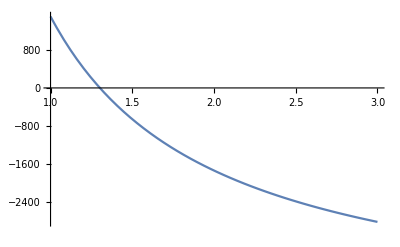

```mathematica
TempRadTor[x_, Γc_,x0_]:=Module[{mum=1 ,A1,γ=1,Rsc, Ts=1500},
Rsc=1PC;
A1=(Gr MBH mum)/(RGAS Rsc)1/Ts;

(*Print[A1];*)

γ = 1-Γc;

1+A1/4 γ(1/x-1/x0)

]
Plot[
1500*TempRadTor[x,0.995,1],{x,1,3}
]
```

```mathematica
13.6/MP CL^3/(α κ^3)(8 Pi/3)^2(Gr MBH/R^3)^(-1/2)Mdot^-2/.{R-> 0.1PC, α->0.1, Mdot->10^-2 MsolYr,κ->10}
```

1.81895×10^18

Convective flux

```mathematica
Vtherm[T_]:= Module[{μ=1},(RGAS/μ T)^(1/2)];
OmegaOrb[r_,M_]:=√(Gr M) r^(-3/2);

VelocOrb[r_,M_]:=√(Gr M) r^(-1/2);

GravAccel[r_,M_]:=Gr M r^-2;

CpecificHeatCp[n_,T_]:=RGAS((1+(4ARAD T^3)/(3n MP RGAS))^2+3(0.5+(4ARAD T^3)/(3n MP RGAS)))

DDrhoT[n_, T_]:=Module[{mum, Pg, Pr, ρ=MP n},
mum = 1.;
Pg=ρ RGAS T/mum;
Pr=ARAD T^4/3;

(*Print[Pr,"  ", Pg];*)

-ρ/T(1+4 Pr/Pg) 
  ]
```

```mathematica
DDrhoT=.
```

```mathematica
0.1 Subscript[f, 0.1](4Pi CL Gr MBH/KPE)
SGB 1500^4 PC PC 0.1
```

1.24949×10^44 f_0.1

2.73285×10^44

```mathematica
ClearAll[Eq, Hc, v, n,ρ,rho, δl, R0, g, gg, gacc, dRho,Cp, rsp,T,vconv]
Eq = (ρ^2 v^3 Cp)/(δl gg dRho);
v = Solve[Eq==Hc, v ][[1]][[1]][[2]]//FullSimplify

CF = 0.01; (*Covering Fraction*)

n=10^9;
T= 1500;
R0=0.1PC;
gacc= GravAccel[r,MBH];

Cp = CpecificHeatCp[n, T];

vconv= v/.{Hc->SGB T^4, gg->gacc, δl->CF r   , dRho->-DDrhoT[n, T]}/.{r-> R0, ρ->n MP};

vconv/VelocOrb[R0,MBH]
```

(dRho^(1/3) gg^(1/3) Hc^(1/3) δl^(1/3))/(Cp^(1/3) ρ^(2/3))

0.944852

```mathematica
DDrhoT[ 10^9, 1500]
```

-2.74207×10^-16

```mathematica
ConvectiveFlux[]
```